## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.2; qscal=0.3; Q=0.95;
```

```mathematica
winit=(0.2-0.00005*I)
```

0.2-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.249608-4.94708×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.217184

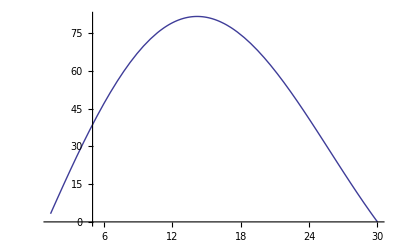

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.2+0.000005*I);
ie=0;While[ie<151,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,150}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,150}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-4.94714×10^-8},{30.2,-4.687×10^-8},{30.4,-4.44276×10^-8},{30.6,-4.21084×10^-8},{30.8,-3.9928×10^-8},{31.,-3.78709×10^-8},{31.2,-3.59294×10^-8},{31.4,-3.40946×10^-8},{31.6,-3.23614×10^-8},{31.8,-3.0724×10^-8},{32.,-2.91766×10^-8},{32.2,-2.77128×10^-8},{32.4,-2.63289×10^-8},{32.6,-2.50182×10^-8},{32.8,-2.37786×10^-8},{33.,-2.26025×10^-8},{33.2,-2.14936×10^-8},{33.4,-2.0441×10^-8},{33.6,-1.9441×10^-8},{33.8,-1.84943×10^-8},{34.,-1.76014×10^-8},{34.2,-1.67497×10^-8},{34.4,-1.59437×10^-8},{34.6,-1.51786×10^-8},{34.8,-1.44529×10^-8},{35.,-1.37635×10^-8},{35.2,-1.31093×10^-8},{35.4,-1.24879×10^-8},{35.6,-1.18977×10^-8},{35.8,-1.13371×10^-8},{36.,-1.08105×10^-8},{36.2,-1.02974×10^-8},{36.4,-9.81567×10^-9},{36.6,-9.35766×10^-9},{36.8,-8.9212×10^-9},{37.,-8.5077×10^-9},{37.2,-8.11306×10^-9},{37.4,-7.73767×10^-9},{37.6,-7.38034×10^-9},{37.8,-7.04035×10^-9},{38.,-6.71614×10^-9},{38.2,-6.40755×10^-9},{38.4,-6.1131×10^-9},{38.6,-5.83301×10^-9},{38.8,-5.56622×10^-9},{39.,-5.31225×10^-9},{39.2,-5.06933×10^-9},{39.4,-4.8386×10^-9},{39.6,-4.61805×10^-9},{39.8,-4.40791×10^-9},{40.,-4.2069×10^-9},{40.2,-4.01079×10^-9},{40.4,-3.83294×10^-9},{40.6,-3.65885×10^-9},{40.8,-3.49249×10^-9},{41.,-3.33377×10^-9},{41.2,-3.18228×10^-9},{41.4,-3.03791×10^-9},{41.6,-2.89955×10^-9},{41.8,-2.76757×10^-9},{42.,-2.64163×10^-9},{42.2,-2.52145×10^-9},{42.4,-2.40622×10^-9},{42.6,-2.2964×10^-9},{42.8,-2.19137×10^-9},{43.,-2.091×10^-9},{43.2,-1.99513×10^-9},{43.4,-1.90327×10^-9},{43.6,-1.8159×10^-9},{43.8,-1.73208×10^-9},{44.,-1.65177×10^-9},{44.2,-1.5754×10^-9},{44.4,-1.50221×10^-9},{44.6,-1.43203×10^-9},{44.8,-1.36504×10^-9},{45.,-1.30108×10^-9},{45.2,-1.2398×10^-9},{45.4,-1.18117×10^-9},{45.6,-1.12509×10^-9},{45.8,-1.07143×10^-9},{46.,-1.02×10^-9},{46.2,-9.709×10^-10},{46.4,-9.24228×10^-10},{46.6,-8.79037×10^-10},{46.8,-8.36128×10^-10},{47.,-7.96315×10^-10},{47.2,-7.55315×10^-10},{47.4,-7.17591×10^-10},{47.6,-6.81522×10^-10},{47.8,-6.46964×10^-10},{48.,-6.13917×10^-10},{48.2,-5.82207×10^-10},{48.4,-5.51908×10^-10},{48.6,-5.22911×10^-10},{48.8,-4.95171×10^-10},{49.,-4.68594×10^-10},{49.2,-4.45047×10^-10},{49.4,-4.18837×10^-10},{49.6,-3.95548×10^-10},{49.8,-3.7326×10^-10},{50.,-3.51912×10^-10},{50.2,-3.31495×10^-10},{50.4,-3.11979×10^-10},{50.6,-2.93478×10^-10},{50.8,-2.75367×10^-10},{51.,-2.58213×10^-10},{51.2,-2.41863×10^-10},{51.4,-2.25702×10^-10},{51.6,-2.11183×10^-10},{51.8,-1.96864×10^-10},{52.,-1.83151×10^-10},{52.2,-1.70294×10^-10},{52.4,-1.57398×10^-10},{52.6,-1.45483×10^-10},{52.8,-1.34006×10^-10},{53.,-1.23038×10^-10},{53.2,-1.12563×10^-10},{53.4,-1.02537×10^-10},{53.6,-9.29608×10^-11},{53.8,-8.38118×10^-11},{54.,-7.51189×10^-11},{54.2,-6.6723×10^-11},{54.4,-5.87457×10^-11},{54.6,-5.08202×10^-11},{54.8,-4.38717×10^-11},{55.,-3.69017×10^-11},{55.2,-3.03152×10^-11},{55.4,-2.40026×10^-11},{55.6,-1.79852×10^-11},{55.8,-1.23273×10^-11},{56.,-6.77424×10^-12},{56.2,-1.55794×10^-12},{56.4,3.41669×10^-12},{56.6,8.13551×10^-12},{56.8,1.30985×10^-11},{57.,1.69181×10^-11},{57.2,2.09944×10^-11},{57.4,2.48674×10^-11},{57.6,2.85482×10^-11},{57.8,3.20144×10^-11},{58.,3.53635×10^-11},{58.2,3.8529×10^-11},{58.4,4.134×10^-11},{58.6,4.43298×10^-11},{58.8,4.70615×10^-11},{59.,4.95223×10^-11},{59.2,5.19524×10^-11},{59.4,5.42185×10^-11},{59.6,5.63614×10^-11},{59.8,5.83789×10^-11},{60.,6.02883×10^-11}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.2+0.000005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

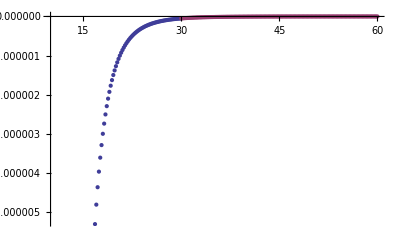

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

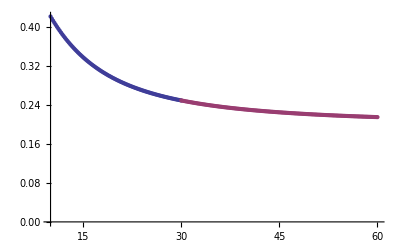

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.95/q=0.3/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.95/q=0.3/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.95/q=0.3/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.95/q=0.3/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```